```mathematica
mgo=GroupOrder[MonsterGroupM[]]
```

808017424794512875886459904961710757005754368000000000

```mathematica
FactorInteger[mgo]
```

{{2,46},{3,20},{5,9},{7,6},{11,2},{13,3},{17,1},{19,1},{23,1},{29,1},{31,1},{41,1},{47,1},{59,1},{71,1}}

```mathematica
NextPrime[71]
```

73

```mathematica
Table[Length[IntegerDigits[mgo,i]],{i,2,73}]
```

{180,113,90,78,70,64,60,57,54,52,50,49,48,46,45,44,43,43,42,41,41,40,40,39,39,38,38,37,37,37,36,36,36,35,35,35,35,34,34,34,34,34,33,33,33,33,33,32,32,32,32,32,32,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,29}

```mathematica
Select[%,¬PrimeQ[#]&]
```

{180,90,78,70,64,60,57,54,52,50,49,48,46,45,44,42,40,40,39,39,38,38,36,36,36,35,35,35,35,34,34,34,34,34,33,33,33,33,33,32,32,32,32,32,32,30,30,30,30,30,30,30,30,30,30}

```mathematica
Select[Out[90],dupfree]
```

{180,90,78,70,64,60,57,54,52,50,49,48,46,45,44,42,40,40,39,39,38,38,36,36,36,35,35,35,35,34,34,34,34,34,33,33,33,33,33,32,32,32,32,32,32,30,30,30,30,30,30,30,30,30,30}

```mathematica
dupfree[x_]:=Or@@Map[DuplicateFreeQ[Partition[IntegerDigits[mgo,x],#]]&,Divisors[x]]
```

```mathematica
dupfree2[x_]:=Map[list2graph,Select[Map[FromDigits[#,x]&,Select[Map[Partition[IntegerDigits[mgo,x],#]&,Divisors[x]],DuplicateFreeQ],{2}],Length[#]>3&]]
dupfree3[x_]:=Map[list2graph,DeleteCases[Select[Map[FromDigits[#,x]&,Select[Map[Partition[IntegerDigits[mgo,x],#]&,Divisors[x]],DuplicateFreeQ],{2}],Length[#]>3&],0]]

dupfree2[Out[98][[1]]]
```

{{114088830795→114088830795,114088830795→44763152838,114088830795→182480357376,114088830795→0,44763152838→114088830795,44763152838→44763152838,44763152838→182480357376,44763152838→0,182480357376→114088830795,182480357376→44763152838,182480357376→182480357376,182480357376→0,0→114088830795,0→44763152838,0→182480357376,0→0},{20535989543142→20535989543142,20535989543142→16967480832000,20535989543142→0,21812743982489→21812743982489,21812743982489→0,16967480832000→20535989543142,16967480832000→16967480832000,16967480832000→0,0→20535989543142,0→21812743982489,0→16967480832000,0→0}}

```mathematica
Out[98]
```

78

```mathematica
dupfreeaux[x_]:=GraphPlot[Select[dupfree3[x],#[[1]]≠0&&#[[2]]≠0&]]
dupfreeaux[Out[98]]
```

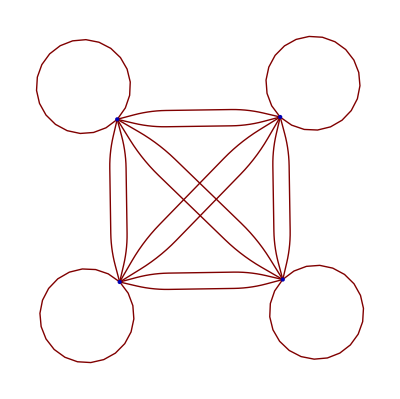
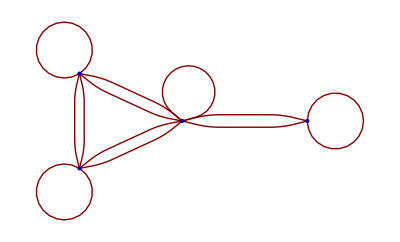

```mathematica
Map[GraphPlot,%]
```

```mathematica
list2graph[list_]:=DeleteCases[Flatten[Table[Piecewise[{{0, CoprimeQ[list[[i]],list[[j]]]}, {list[[i]]->list[[j]], ¬CoprimeQ[list[[i]],list[[j]]]}}],{i,1,Length[list]},{j,1,Length[list]}]],0]
list3graph[list_]:=DeleteCases[Flatten[Table[Piecewise[{{0, ¬CoprimeQ[list[[i]],list[[j]]]}, {list[[i]]->list[[j]], CoprimeQ[list[[i]],list[[j]]]}}],{i,1,Length[list]},{j,1,Length[list]}]],0]
```

```mathematica
Map[dupfree2,Out[98]]
```

{1,53,{{4360543→4360543,4360543→0,453584→453584,453584→20825586,453584→6026400,453584→0,20825586→453584,20825586→20825586,20825586→20126457,20825586→6026400,20825586→0,8,6026400→20126457,6026400→6026400,6026400→0,0→4360543,0→453584,0→20825586,0→20126457,0→17333077,0→6026400,0→0},1}}
 |  |  |  |

```mathematica
Flatten[%,1]
```

{1}
 |  |  |  |

```mathematica
Length[Out[123]]
```

89

```mathematica
Select[Out[123],Length[#]>30&][[10]]
```

{1767230→1767230,1767230→501708,1767230→1817520,1767230→1561525,1767230→3498476,1767230→2000164,1767230→1317888,501708→1767230,501708→501708,501708→1132059,501708→1817520,501708→3498476,501708→2000164,501708→1317888,1132059→501708,1132059→1132059,1132059→1817520,1132059→1317888,1817520→1767230,1817520→501708,1817520→1132059,1817520→1817520,1817520→1561525,1817520→3498476,1817520→2000164,1817520→1317888,1561525→1767230,1561525→1817520,1561525→1561525,3498476→1767230,3498476→501708,3498476→1817520,3498476→3498476,3498476→2000164,3498476→1317888,2000164→1767230,2000164→501708,2000164→1817520,2000164→3498476,2000164→2000164,2000164→1317888,1317888→1767230,1317888→501708,1317888→1132059,1317888→1817520,1317888→3498476,1317888→2000164,1317888→1317888}

```mathematica
Length[%]
```

48

```mathematica
MaximalBy[Out[123],Length]
```

```mathematica
{{68->68,68->842,68->312,68->1018,68->368,68->418,68->92,68->852,68->108,68->1076,68->612,842->68,842->842,842->312,842->1018,842->368,842->418,842->92,842->852,842->108,842->1076,842->612,312->68,312->842,312->312,312->1018,312->368,312->418,312->1137,312->92,312->852,312->108,312->1076,312->747,312->603,312->612,1018->68,1018->842,1018->312,1018->1018,1018->368,1018->418,1018->92,1018->852,1018->108,1018->1076,1018->612,368->68,368->842,368->312,368->1018,368->368,368->418,368->92,368->852,368->667,368->108,368->1076,368->612,418->68,418->842,418->312,418->1018,418->368,418->418,418->92,418->852,418->108,418->1076,418->612,1137->312,1137->1137,1137->852,1137->108,1137->747,1137->603,1137->612,92->68,92->842,92->312,92->1018,92->368,92->418,92->92,92->852,92->667,92->108,92->1076,92->612,852->68,852->842,852->312,852->1018,852->368,852->418,852->1137,852->92,852->852,852->108,852->1076,852->747,852->603,852->612,1063->1063,329->329,667->368,667->92,667->667,108->68,108->842,108->312,108->1018,108->368,108->418,108->1137,108->92,108->852,108->108,108->1076,108->747,108->603,108->612,83->83,83->747,1076->68,1076->842,1076->312,1076->1018,1076->368,1076->418,1076->92,1076->852,1076->108,1076->1076,1076->612,747->312,747->1137,747->852,747->108,747->83,747->747,747->603,747->612,603->312,603->1137,603->852,603->108,603->747,603->603,603->612,612->68,612->842,612->312,612->1018,612->368,612->418,612->1137,612->92,612->852,612->108,612->1076,612->747,612->603,612->612},{68->68,68->842,68->312,68->1018,68->368,68->418,68->92,68->852,68->108,68->1076,68->612,842->68,842->842,842->312,842->1018,842->368,842->418,842->92,842->852,842->108,842->1076,842->612,312->68,312->842,312->312,312->1018,312->368,312->418,312->1137,312->92,312->852,312->108,312->1076,312->747,312->603,312->612,1018->68,1018->842,1018->312,1018->1018,1018->368,1018->418,1018->92,1018->852,1018->108,1018->1076,1018->612,368->68,368->842,368->312,368->1018,368->368,368->418,368->92,368->852,368->667,368->108,368->1076,368->612,418->68,418->842,418->312,418->1018,418->368,418->418,418->92,418->852,418->108,418->1076,418->612,1137->312,1137->1137,1137->852,1137->108,1137->747,1137->603,1137->612,92->68,92->842,92->312,92->1018,92->368,92->418,92->92,92->852,92->667,92->108,92->1076,92->612,852->68,852->842,852->312,852->1018,852->368,852->418,852->1137,852->92,852->852,852->108,852->1076,852->747,852->603,852->612,1063->1063,329->329,667->368,667->92,667->667,108->68,108->842,108->312,108->1018,108->368,108->418,108->1137,108->92,108->852,108->108,108->1076,108->747,108->603,108->612,83->83,83->747,1076->68,1076->842,1076->312,1076->1018,1076->368,1076->418,1076->92,1076->852,1076->108,1076->1076,1076->612,747->312,747->1137,747->852,747->108,747->83,747->747,747->603,747->612,603->312,603->1137,603->852,603->108,603->747,603->603,603->612,612->68,612->842,612->312,612->1018,612->368,612->418,612->1137,612->92,612->852,612->108,612->1076,612->747,612->603,612->612},{68->68,68->842,68->312,68->1018,68->368,68->418,68->92,68->852,68->108,68->1076,68->612,842->68,842->842,842->312,842->1018,842->368,842->418,842->92,842->852,842->108,842->1076,842->612,312->68,312->842,312->312,312->1018,312->368,312->418,312->1137,312->92,312->852,312->108,312->1076,312->747,312->603,312->612,1018->68,1018->842,1018->312,1018->1018,1018->368,1018->418,1018->92,1018->852,1018->108,1018->1076,1018->612,368->68,368->842,368->312,368->1018,368->368,368->418,368->92,368->852,368->667,368->108,368->1076,368->612,418->68,418->842,418->312,418->1018,418->368,418->418,418->92,418->852,418->108,418->1076,418->612,1137->312,1137->1137,1137->852,1137->108,1137->747,1137->603,1137->612,92->68,92->842,92->312,92->1018,92->368,92->418,92->92,92->852,92->667,92->108,92->1076,92->612,852->68,852->842,852->312,852->1018,852->368,852->418,852->1137,852->92,852->852,852->108,852->1076,852->747,852->603,852->612,1063->1063,329->329,667->368,667->92,667->667,108->68,108->842,108->312,108->1018,108->368,108->418,108->1137,108->92,108->852,108->108,108->1076,108->747,108->603,108->612,83->83,83->747,1076->68,1076->842,1076->312,1076->1018,1076->368,1076->418,1076->92,1076->852,1076->108,1076->1076,1076->612,747->312,747->1137,747->852,747->108,747->83,747->747,747->603,747->612,603->312,603->1137,603->852,603->108,603->747,603->603,603->612,612->68,612->842,612->312,612->1018,612->368,612->418,612->1137,612->92,612->852,612->108,612->1076,612->747,612->603,612->612},{68->68,68->842,68->312,68->1018,68->368,68->418,68->92,68->852,68->108,68->1076,68->612,842->68,842->842,842->312,842->1018,842->368,842->418,842->92,842->852,842->108,842->1076,842->612,312->68,312->842,312->312,312->1018,312->368,312->418,312->1137,312->92,312->852,312->108,312->1076,312->747,312->603,312->612,1018->68,1018->842,1018->312,1018->1018,1018->368,1018->418,1018->92,1018->852,1018->108,1018->1076,1018->612,368->68,368->842,368->312,368->1018,368->368,368->418,368->92,368->852,368->667,368->108,368->1076,368->612,418->68,418->842,418->312,418->1018,418->368,418->418,418->92,418->852,418->108,418->1076,418->612,1137->312,1137->1137,1137->852,1137->108,1137->747,1137->603,1137->612,92->68,92->842,92->312,92->1018,92->368,92->418,92->92,92->852,92->667,92->108,92->1076,92->612,852->68,852->842,852->312,852->1018,852->368,852->418,852->1137,852->92,852->852,852->108,852->1076,852->747,852->603,852->612,1063->1063,329->329,667->368,667->92,667->667,108->68,108->842,108->312,108->1018,108->368,108->418,108->1137,108->92,108->852,108->108,108->1076,108->747,108->603,108->612,83->83,83->747,1076->68,1076->842,1076->312,1076->1018,1076->368,1076->418,1076->92,1076->852,1076->108,1076->1076,1076->612,747->312,747->1137,747->852,747->108,747->83,747->747,747->603,747->612,603->312,603->1137,603->852,603->108,603->747,603->603,603->612,612->68,612->842,612->312,612->1018,612->368,612->418,612->1137,612->92,612->852,612->108,612->1076,612->747,612->603,612->612},{68->68,68->842,68->312,68->1018,68->368,68->418,68->92,68->852,68->108,68->1076,68->612,842->68,842->842,842->312,842->1018,842->368,842->418,842->92,842->852,842->108,842->1076,842->612,312->68,312->842,312->312,312->1018,312->368,312->418,312->1137,312->92,312->852,312->108,312->1076,312->747,312->603,312->612,1018->68,1018->842,1018->312,1018->1018,1018->368,1018->418,1018->92,1018->852,1018->108,1018->1076,1018->612,368->68,368->842,368->312,368->1018,368->368,368->418,368->92,368->852,368->667,368->108,368->1076,368->612,418->68,418->842,418->312,418->1018,418->368,418->418,418->92,418->852,418->108,418->1076,418->612,1137->312,1137->1137,1137->852,1137->108,1137->747,1137->603,1137->612,92->68,92->842,92->312,92->1018,92->368,92->418,92->92,92->852,92->667,92->108,92->1076,92->612,852->68,852->842,852->312,852->1018,852->368,852->418,852->1137,852->92,852->852,852->108,852->1076,852->747,852->603,852->612,1063->1063,329->329,667->368,667->92,667->667,108->68,108->842,108->312,108->1018,108->368,108->418,108->1137,108->92,108->852,108->108,108->1076,108->747,108->603,108->612,83->83,83->747,1076->68,1076->842,1076->312,1076->1018,1076->368,1076->418,1076->92,1076->852,1076->108,1076->1076,1076->612,747->312,747->1137,747->852,747->108,747->83,747->747,747->603,747->612,603->312,603->1137,603->852,603->108,603->747,603->603,603->612,612->68,612->842,612->312,612->1018,612->368,612->418,612->1137,612->92,612->852,612->108,612->1076,612->747,612->603,612->612}}[[1]]
```

{68→68,68→842,68→312,68→1018,68→368,68→418,68→92,68→852,68→108,68→1076,68→612,842→68,842→842,842→312,842→1018,842→368,842→418,842→92,842→852,842→108,842→1076,842→612,312→68,312→842,312→312,312→1018,312→368,312→418,312→1137,312→92,312→852,312→108,312→1076,312→747,312→603,312→612,1018→68,1018→842,1018→312,1018→1018,1018→368,1018→418,1018→92,1018→852,1018→108,1018→1076,1018→612,368→68,368→842,368→312,368→1018,368→368,368→418,368→92,368→852,368→667,368→108,368→1076,368→612,418→68,418→842,418→312,418→1018,418→368,418→418,418→92,418→852,418→108,418→1076,418→612,1137→312,1137→1137,1137→852,1137→108,1137→747,1137→603,1137→612,92→68,92→842,92→312,92→1018,92→368,92→418,92→92,92→852,92→667,92→108,92→1076,92→612,852→68,852→842,852→312,852→1018,852→368,852→418,852→1137,852→92,852→852,852→108,852→1076,852→747,852→603,852→612,1063→1063,329→329,667→368,667→92,667→667,108→68,108→842,108→312,108→1018,108→368,108→418,108→1137,108→92,108→852,108→108,108→1076,108→747,108→603,108→612,83→83,83→747,1076→68,1076→842,1076→312,1076→1018,1076→368,1076→418,1076→92,1076→852,1076→108,1076→1076,1076→612,747→312,747→1137,747→852,747→108,747→83,747→747,747→603,747→612,603→312,603→1137,603→852,603→108,603→747,603→603,603→612,612→68,612→842,612→312,612→1018,612→368,612→418,612→1137,612→92,612→852,612→108,612→1076,612→747,612→603,612→612}

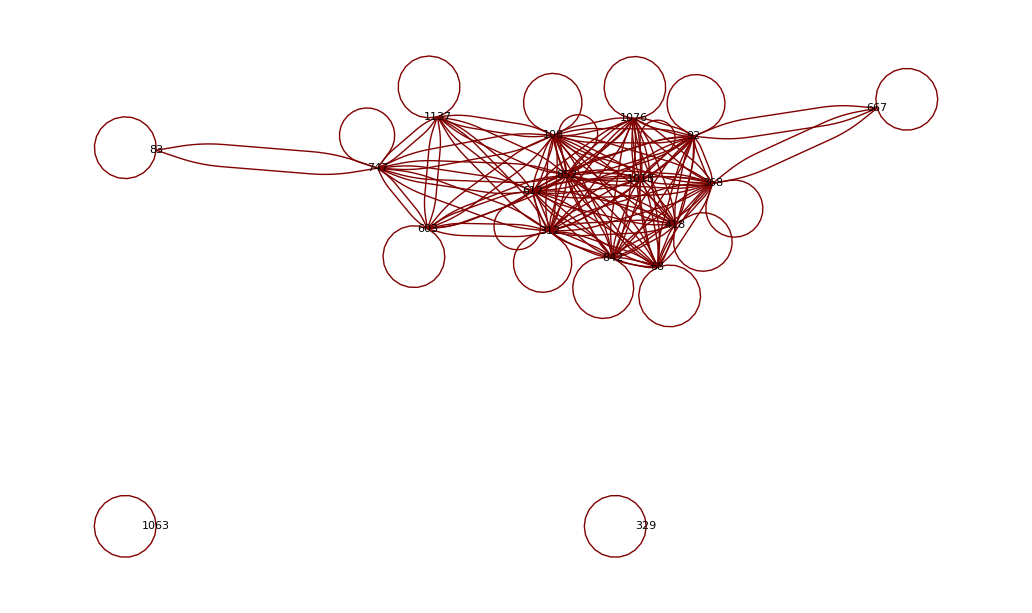

```mathematica
GraphPlot[%,VertexLabeling->True]
```

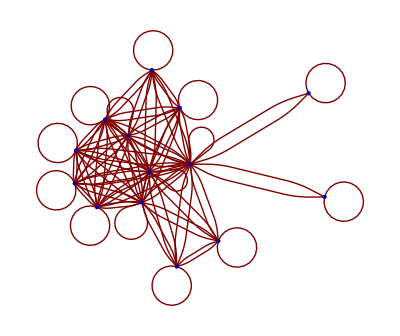
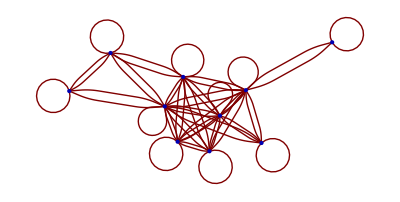
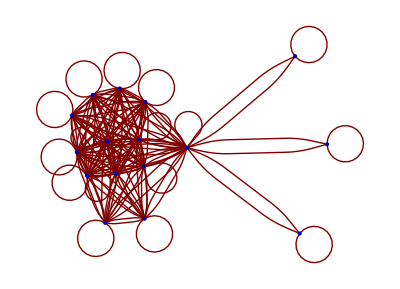
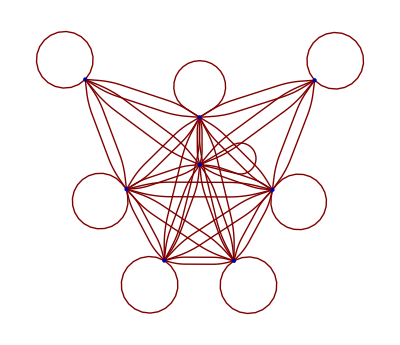
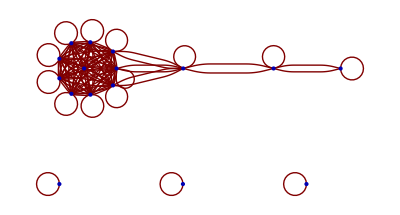
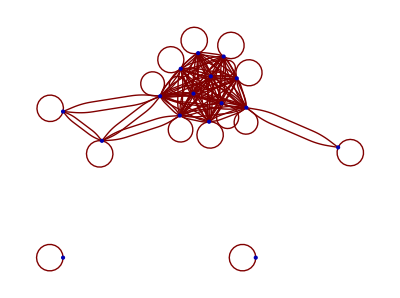
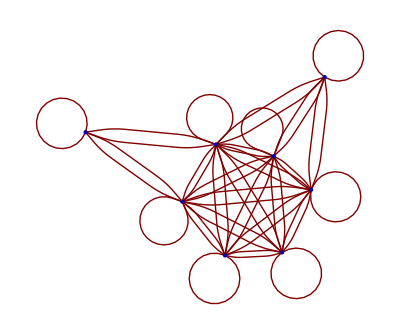
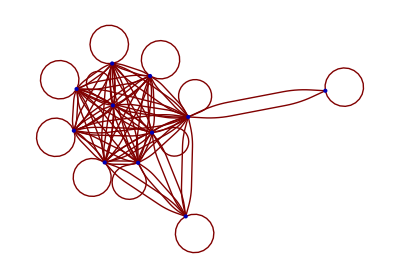
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[GraphPlot,Select[Out[123],Length[#]>45&]]
```

```mathematica
DeleteDuplicates[
```

```mathematica
GraphPlot[Out[123][[2]]]
```

-Graphics-

```mathematica
Divisible[6,3]
```

True

```mathematica
Map[Total[Map[Boole[Divisible[mgo,#]]&,DeleteCases[DeleteDuplicates[Flatten[Map[{#[[1]],#[[2]]}&,#]]],0]]]&,Out[123]]
```

{0,0,0,1,4,0,0,0,0,0,1,1,0,1,2,0,9,1,0,0,0,0,7,0,9,1,2,0,0,2,0,1,2,0,1,1,1,9,9,1,1,1,1,1,1,0,1,0,1,0,1,0,1,10,10,10,10,10,3,3,3,3,3,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}